```mathematica
Quit[]
```

```mathematica
(* True structure factor *)
Sk0[x_]:=nb(A+x^2)/(1+x^2)
```

```mathematica
(* correction factor for spatial descretization *)
G[x_]:=Sin[Sqrt[a/b]x/2]^2/(Sqrt[a/b]x/2)^2
```

```mathematica
(* unsplit forward Euler *)
(* temporal_integrator = -1 *)
L=-r(1+g x^2);
KK=2 nb r(A+g x^2);
M=1+L a/r;
NN=KK a/r;
Sk=NN/(1-M M);
SkUnsplitForwardEuler[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* unsplit first-order implicit scheme [diffusion:Crank-Nicolson, reaction:external source] *)
(* not implemented in our codes *)
M=(1-g x^2a/2-a)/(1+g x^2 a/2);
NN=2nb a(A+ g x^2 )/(1+g x^2 a/2)^2;
Sk=Simplify[NN/(1-M M)];
SkUnsplitFirstOrderImplicit[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* unsplit explicit midpoint predictor-corrector *)
(* temporal_integrator = -2 *)
L=-r(1+g x^2);
KK=2 nb r(A+g x^2);
M=1+L a/r+L^2/2(a/r)^2;
NN=1/2(a/r)KK(1+(1+(a/r)L)^2);
Sk=NN/(1-M M);
SkUnsplitExplicitMidpoint[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* unsplit implicit trapezoidal predictor-corrector *)
(* not implemented in our codes *)
A1=(1-g x^2a/2-a)/(1+g x^2 a/2);
A2=(1-g x^2a/2-a/2)/(1+g x^2 a/2);
A3=(-a/2)/(1+g x^2 a/2);
B1B1=2nb a g x^2 /(1+g x^2 a/2)^2;
B2B2=2nb a A/(1+g x^2 a/2)^2;
M=A2+A1 A3;
NN=(A3+1)^2(B1B1+B2B2);
Sk=Simplify[NN/(1-M M)];
SkUnsplitImplicitTrapezoidal[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* unsplit implicit midpoint scheme *)
(* temporal_integrator = -4 *)
A1=(1-(1/2-w1)g x^2 a-a/2)/(1+w1 g x^2 a);
B1=Sqrt[nb g x^2 a]/(1+w1 g x^2 a);
B2=Sqrt[A nb a]/(1+w1 g x^2 a);
A2=(1-g x^2 a/2)/(1+g x^2 a/2);
A3=-a/(1+g x^2 a/2);
B3=Sqrt[nb g x^2 a]/(1+g x^2 a/2);
B4=Sqrt[A nb a]/(1+g x^2 a/2);
M=A2+A1 A3;
NN=(A3 B1+B3)^2+B3^2+(A3 B2+B4)^2+B4^2;
Sk=NN/(1-M M);
SkUnsplitImplicitMidpoint[x_,w1_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* R/2+D+R/2, D=CN, R=Euler *)
(* temporal_integrator = 1, diffusion_type = 1, reaction_type = 0 *)
MR=1-a/2;
NRNR=A nb a;
LD=-r g x^2;
KDKD=2 nb r g x^2;
MD=(1+(a/r)/2 LD)/(1-(a/r)/2LD);
NDND=KDKD(a/r)/(1-(a/r)/2LD)^2;
M=MR^2 MD;
NN=MR^2MD^2NRNR+MR^2NDND+NRNR;
Sk=NN/(1-M M);
SkSplit1Diff1React0[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* R/2+D+R/2, D=CN, R=PC *)
(* temporal_integrator = 1, diffusion_type = 1, reaction_type = 1 *)
MR=1-a/2+a^2/8;
NRNR=A nb a/2(1+(1-a/2)^2);
LD=-r g x^2;
KDKD=2 nb r g x^2;
MD=(1+(a/r)/2 LD)/(1-(a/r)/2LD);
NDND=KDKD(a/r)/(1-(a/r)/2LD)^2;
M=MR^2 MD;
NN=MR^2MD^2NRNR+MR^2NDND+NRNR;
Sk=NN/(1-M M);
SkSplit1Diff1React1[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* D/2+R+D/2, D=CN, R=Euler *)
(* temporal_integrator = 2, diffusion_type = 1, reaction_type = 0 *)
LD=-r g x^2;
KDKD=2 nb r g x^2;
MD=(1+(a/r)/4 LD)/(1-(a/r)/4LD);
NDND=KDKD(a/r)/2/(1-(a/r)/4 LD)^2;
MR=1-a;
NRNR=2 nb A a;
M=MD^2MR;
NN=MD^2MR^2NDND+MD^2NRNR+NDND;
Sk=NN/(1-M M);
SkSplit2Diff1React0[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* D/2+R+D/2, D=CN, R=PC *)
(* temporal_integrator = 2, diffusion_type = 1, reaction_type = 1 *)
LD=-r g x^2;
KDKD=2 nb r g x^2;
MD=(1+(a/r)/4 LD)/(1-(a/r)/4LD);
NDND=KDKD(a/r)/2/(1-(a/r)/4 LD)^2;
MR=1-a+a^2/2;
NRNR=nb A a(1+(1-a)^2);
M=MD^2MR;
NN=MD^2MR^2NDND+MD^2NRNR+NDND;
Sk=NN/(1-M M);
SkSplit2Diff1React1[x_]:=Evaluate[Sk/.g->G[x]]
```

```mathematica
(* PLOT1 *)
```

```mathematica
nbVal=1;AVal=2;
S0[x_]:=Evaluate[Sk0[x]/.{nb->nbVal,A->AVal}]
S1[x_,alpha_,beta_]:=Evaluate[SkUnsplitForwardEuler[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S2[x_,alpha_,beta_]:=Evaluate[SkUnsplitFirstOrderImplicit[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S3[x_,alpha_,beta_]:=Evaluate[SkUnsplitExplicitMidpoint[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S4[x_,alpha_,beta_]:=Evaluate[SkUnsplitImplicitTrapezoidal[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S5[x_,alpha_,beta_]:=Evaluate[SkUnsplitImplicitMidpoint[x,1/2]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S6[x_,alpha_,beta_]:=Evaluate[SkSplit1Diff1React0[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S7[x_,alpha_,beta_]:=Evaluate[SkSplit1Diff1React1[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S8[x_,alpha_,beta_]:=Evaluate[SkSplit2Diff1React0[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
S9[x_,alpha_,beta_]:=Evaluate[SkSplit2Diff1React1[x]/.{a->alpha,b->beta,nb->nbVal,A->AVal}]
```

```mathematica
xMax[alpha_,beta_]:=Sqrt[beta/alpha]Pi
```

```mathematica
alpha0=0.3;
Manipulate[Plot[{S4[x,alpha0,beta],S5[x,alpha0,beta],S0[x]},{x,-xMax[alpha0,beta],xMax[alpha0,beta]},PlotRange->{0.5nbVal,1.25S0[0]},PlotStyle->{Red,Blue,{Black,Dashed}}],{beta,1,10}]
```

```mathematica
beta0=3;
Manipulate[Plot[{S4[x,alpha,beta0],S5[x,alpha,beta0],S0[x]},{x,-xMax[alpha,beta0],xMax[alpha,beta0]},PlotRange->{0.5nbVal,1.25S0[0]},PlotStyle->{Red,Blue,{Black,Dashed}}],{alpha,0.01,1}]
```

```mathematica
(* PLOT2 *)
```

```mathematica
k1=1.5;k2=0.6;k3=2.05;k4=2.95;
d[n_]:=-k2 n^3+k1 n^2-k4 n+k3 
DG[n_]:=(k2 n^3+k1 n^2+k4 n+k3)/2
NSolve[d[n]==0,n]
```

{{n→0.75-1.68943 ⅈ},{n→0.75+1.68943 ⅈ},{n→1.}}

```mathematica
n0=1;
r=-d'[n0]
D0=DG[n0]
```

1.75

3.55

```mathematica
dt=0.01;dx=0.25;
rm=0.1/r/dt (* rate_multiplier *)
chi=0.25 dx^2/dt (* diffusion coefficient *)
alpha=rm r dt
beta=chi dt/dx^2
```

5.71429

1.5625

0.1

0.25

```mathematica
S0[x_]:=Evaluate[Sk0[x]/.{nb->n0,A->D0/n0/r}]
S1[x_]:=Evaluate[SkUnsplitForwardEuler[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S2[x_]:=Evaluate[SkUnsplitFirstOrderImplicit[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S3[x_]:=Evaluate[SkUnsplitExplicitMidpoint[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S4[x_]:=Evaluate[SkUnsplitImplicitTrapezoidal[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S5[x_]:=Evaluate[SkUnsplitImplicitMidpoint[x,1/2]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S6[x_]:=Evaluate[SkSplit1Diff1React0[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S7[x_]:=Evaluate[SkSplit1Diff1React1[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S8[x_]:=Evaluate[SkSplit2Diff1React0[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S9[x_]:=Evaluate[SkSplit2Diff1React1[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
```

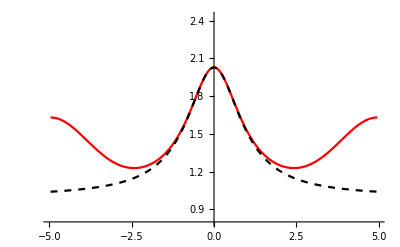

```mathematica
xmax=Sqrt[beta/alpha]Pi;
Plot[{S3[x],S0[x]},{x,-xmax,xmax},PlotRange->{0.8n0,1.2S0[0]},PlotStyle->{Red,{Black,Dashed}}]
```

```mathematica
(* Print S(k) *)
```

```mathematica
Npts=100;
xmax=Sqrt[beta/alpha]Pi;
Table[{k/Npts xmax,S3[k/Npts xmax]},{k,-Npts,Npts}]//MatrixForm
```

(-4.96729 | 1.63077
-4.91762 | 1.63031
-4.86795 | 1.6289
-4.81828 | 1.62657
-4.7686 | 1.62333
-4.71893 | 1.6192
-4.66926 | 1.6142
-4.61958 | 1.60837
-4.56991 | 1.60173
-4.52024 | 1.59432
-4.47056 | 1.58619
-4.42089 | 1.57739
-4.37122 | 1.56796
-4.32155 | 1.55796
-4.27187 | 1.54743
-4.2222 | 1.53644
-4.17253 | 1.52504
-4.12285 | 1.5133
-4.07318 | 1.50126
-4.02351 | 1.48898
-3.97384 | 1.47654
-3.92416 | 1.46397
-3.87449 | 1.45134
-3.82482 | 1.43871
-3.77514 | 1.42612
-3.72547 | 1.41362
-3.6758 | 1.40127
-3.62612 | 1.38911
-3.57645 | 1.37718
-3.52678 | 1.36553
-3.47711 | 1.35418
-3.42743 | 1.34319
-3.37776 | 1.33258
-3.32809 | 1.32238
-3.27841 | 1.31261
-3.22874 | 1.30331
-3.17907 | 1.29449
-3.1294 | 1.28617
-3.07972 | 1.27837
-3.03005 | 1.2711
-2.98038 | 1.26438
-2.9307 | 1.25821
-2.88103 | 1.25261
-2.83136 | 1.24757
-2.78168 | 1.24312
-2.73201 | 1.23924
-2.68234 | 1.23594
-2.63267 | 1.23323
-2.58299 | 1.23111
-2.53332 | 1.22957
-2.48365 | 1.22862
-2.43397 | 1.22826
-2.3843 | 1.2285
-2.33463 | 1.22932
-2.28496 | 1.23074
-2.23528 | 1.23276
-2.18561 | 1.23538
-2.13594 | 1.23861
-2.08626 | 1.24246
-2.03659 | 1.24694
-1.98692 | 1.25205
-1.93724 | 1.25782
-1.88757 | 1.26425
-1.8379 | 1.27137
-1.78823 | 1.27919
-1.73855 | 1.28775
-1.68888 | 1.29706
-1.63921 | 1.30716
-1.58953 | 1.31808
-1.53986 | 1.32985
-1.49019 | 1.34251
-1.44052 | 1.35612
-1.39084 | 1.37069
-1.34117 | 1.3863
-1.2915 | 1.40297
-1.24182 | 1.42075
-1.19215 | 1.4397
-1.14248 | 1.45985
-1.0928 | 1.48125
-1.04313 | 1.50391
-0.993459 | 1.52788
-0.943786 | 1.55315
-0.894113 | 1.57971
-0.84444 | 1.60753
-0.794767 | 1.63654
-0.745094 | 1.66665
-0.695421 | 1.69772
-0.645748 | 1.72955
-0.596075 | 1.7619
-0.546402 | 1.79445
-0.496729 | 1.82685
-0.447056 | 1.85864
-0.397384 | 1.88934
-0.347711 | 1.9184
-0.298038 | 1.94524
-0.248365 | 1.96925
-0.198692 | 1.98987
-0.149019 | 2.00654
-0.0993459 | 2.01881
-0.0496729 | 2.02632
0. | 2.02885
0.0496729 | 2.02632
0.0993459 | 2.01881
0.149019 | 2.00654
0.198692 | 1.98987
0.248365 | 1.96925
0.298038 | 1.94524
0.347711 | 1.9184
0.397384 | 1.88934
0.447056 | 1.85864
0.496729 | 1.82685
0.546402 | 1.79445
0.596075 | 1.7619
0.645748 | 1.72955
0.695421 | 1.69772
0.745094 | 1.66665
0.794767 | 1.63654
0.84444 | 1.60753
0.894113 | 1.57971
0.943786 | 1.55315
0.993459 | 1.52788
1.04313 | 1.50391
1.0928 | 1.48125
1.14248 | 1.45985
1.19215 | 1.4397
1.24182 | 1.42075
1.2915 | 1.40297
1.34117 | 1.3863
1.39084 | 1.37069
1.44052 | 1.35612
1.49019 | 1.34251
1.53986 | 1.32985
1.58953 | 1.31808
1.63921 | 1.30716
1.68888 | 1.29706
1.73855 | 1.28775
1.78823 | 1.27919
1.8379 | 1.27137
1.88757 | 1.26425
1.93724 | 1.25782
1.98692 | 1.25205
2.03659 | 1.24694
2.08626 | 1.24246
2.13594 | 1.23861
2.18561 | 1.23538
2.23528 | 1.23276
2.28496 | 1.23074
2.33463 | 1.22932
2.3843 | 1.2285
2.43397 | 1.22826
2.48365 | 1.22862
2.53332 | 1.22957
2.58299 | 1.23111
2.63267 | 1.23323
2.68234 | 1.23594
2.73201 | 1.23924
2.78168 | 1.24312
2.83136 | 1.24757
2.88103 | 1.25261
2.9307 | 1.25821
2.98038 | 1.26438
3.03005 | 1.2711
3.07972 | 1.27837
3.1294 | 1.28617
3.17907 | 1.29449
3.22874 | 1.30331
3.27841 | 1.31261
3.32809 | 1.32238
3.37776 | 1.33258
3.42743 | 1.34319
3.47711 | 1.35418
3.52678 | 1.36553
3.57645 | 1.37718
3.62612 | 1.38911
3.6758 | 1.40127
3.72547 | 1.41362
3.77514 | 1.42612
3.82482 | 1.43871
3.87449 | 1.45134
3.92416 | 1.46397
3.97384 | 1.47654
4.02351 | 1.48898
4.07318 | 1.50126
4.12285 | 1.5133
4.17253 | 1.52504
4.2222 | 1.53644
4.27187 | 1.54743
4.32155 | 1.55796
4.37122 | 1.56796
4.42089 | 1.57739
4.47056 | 1.58619
4.52024 | 1.59432
4.56991 | 1.60173
4.61958 | 1.60837
4.66926 | 1.6142
4.71893 | 1.6192
4.7686 | 1.62333
4.81828 | 1.62657
4.86795 | 1.6289
4.91762 | 1.63031
4.96729 | 1.63077)

```mathematica
(* PLOT 3 *)
```

```mathematica
(* monomodal, detailed balance not satisfied*)
k1=1.5;k2=0.6;k3=2.05;k4=2.95;
```

```mathematica
(* monomodal, equilibrium *)
k1=1.;k2=1.;k3=1.;k4=1.;
```

```mathematica
d[n_]:=-k2 n^3+k1 n^2-k4 n+k3 
DG[n_]:=(k2 n^3+k1 n^2+k4 n+k3)/2
NSolve[d[n]==0,n]
```

{{n→0.-1. ⅈ},{n→0.+1. ⅈ},{n→1.}}

```mathematica
n0=1;
r=-d'[n0]
D0=DG[n0]
```

2.

2.

```mathematica
dt=2.;
dx=1.;
rm=0.1; (* rate_multiplier *)
chi=1.;(* diffusion coefficient *)
alpha=rm r dt
beta=chi dt/dx^2
```

0.4

2.

```mathematica
S0[x_]:=Evaluate[Sk0[x]/.{nb->n0,A->D0/n0/r}]
S1[x_]:=Evaluate[SkUnsplitForwardEuler[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S2[x_]:=Evaluate[SkUnsplitFirstOrderImplicit[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S3[x_]:=Evaluate[SkUnsplitExplicitMidpoint[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S4[x_]:=Evaluate[SkUnsplitImplicitTrapezoidal[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S5[x_]:=Evaluate[SkUnsplitImplicitMidpoint[x,1/2]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S6[x_]:=Evaluate[SkSplit1Diff1React0[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S7[x_]:=Evaluate[SkSplit1Diff1React1[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S8[x_]:=Evaluate[SkSplit2Diff1React0[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
S9[x_]:=Evaluate[SkSplit2Diff1React1[x]/.{a->alpha,b->beta,nb->n0,A->D0/n0/r}]
```

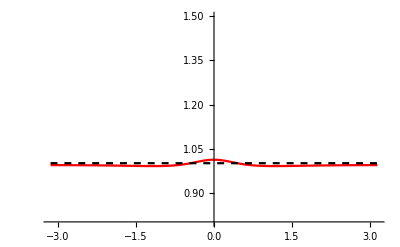

```mathematica
xmax=Pi/dx;
Plot[{S5[Sqrt[chi/r/rm]x],S0[Sqrt[chi/r/rm]x]},{x,-xmax,xmax},PlotRange->{0.8n0,1.5S0[0]},PlotStyle->{Red,{Black,Dashed}}]
```

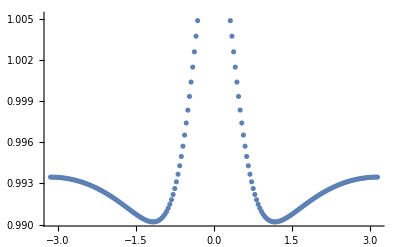

(-3.14159 | 0.993457
-3.11018 | 0.993456
-3.07876 | 0.993453
-3.04734 | 0.993448
-3.01593 | 0.993442
-2.98451 | 0.993433
-2.9531 | 0.993422
-2.92168 | 0.993409
-2.89027 | 0.993394
-2.85885 | 0.993378
-2.82743 | 0.993359
-2.79602 | 0.993338
-2.7646 | 0.993315
-2.73319 | 0.99329
-2.70177 | 0.993263
-2.67035 | 0.993235
-2.63894 | 0.993203
-2.60752 | 0.99317
-2.57611 | 0.993135
-2.54469 | 0.993098
-2.51327 | 0.993058
-2.48186 | 0.993017
-2.45044 | 0.992973
-2.41903 | 0.992927
-2.38761 | 0.992879
-2.35619 | 0.992829
-2.32478 | 0.992776
-2.29336 | 0.992722
-2.26195 | 0.992665
-2.23053 | 0.992606
-2.19911 | 0.992544
-2.1677 | 0.992481
-2.13628 | 0.992415
-2.10487 | 0.992348
-2.07345 | 0.992278
-2.04204 | 0.992206
-2.01062 | 0.992132
-1.9792 | 0.992056
-1.94779 | 0.991978
-1.91637 | 0.991898
-1.88496 | 0.991817
-1.85354 | 0.991734
-1.82212 | 0.991649
-1.79071 | 0.991564
-1.75929 | 0.991477
-1.72788 | 0.991389
-1.69646 | 0.9913
-1.66504 | 0.991211
-1.63363 | 0.991122
-1.60221 | 0.991034
-1.5708 | 0.990946
-1.53938 | 0.990859
-1.50796 | 0.990774
-1.47655 | 0.990691
-1.44513 | 0.990612
-1.41372 | 0.990536
-1.3823 | 0.990465
-1.35088 | 0.990399
-1.31947 | 0.990341
-1.28805 | 0.99029
-1.25664 | 0.990248
-1.22522 | 0.990218
-1.19381 | 0.990199
-1.16239 | 0.990196
-1.13097 | 0.990208
-1.09956 | 0.990239
-1.06814 | 0.990291
-1.03673 | 0.990366
-1.00531 | 0.990468
-0.973894 | 0.990599
-0.942478 | 0.990762
-0.911062 | 0.990961
-0.879646 | 0.9912
-0.84823 | 0.991482
-0.816814 | 0.991811
-0.785398 | 0.99219
-0.753982 | 0.992623
-0.722566 | 0.993114
-0.69115 | 0.993666
-0.659734 | 0.994281
-0.628319 | 0.994961
-0.596903 | 0.995707
-0.565487 | 0.996519
-0.534071 | 0.997397
-0.502655 | 0.998336
-0.471239 | 0.999332
-0.439823 | 1.00038
-0.408407 | 1.00147
-0.376991 | 1.00258
-0.345575 | 1.00372
-0.314159 | 1.00485
-0.282743 | 1.00597
-0.251327 | 1.00704
-0.219911 | 1.00806
-0.188496 | 1.009
-0.15708 | 1.00984
-0.125664 | 1.01056
-0.0942478 | 1.01113
-0.0628319 | 1.01156
-0.0314159 | 1.01182
0. | 1.0119
0.0314159 | 1.01182
0.0628319 | 1.01156
0.0942478 | 1.01113
0.125664 | 1.01056
0.15708 | 1.00984
0.188496 | 1.009
0.219911 | 1.00806
0.251327 | 1.00704
0.282743 | 1.00597
0.314159 | 1.00485
0.345575 | 1.00372
0.376991 | 1.00258
0.408407 | 1.00147
0.439823 | 1.00038
0.471239 | 0.999332
0.502655 | 0.998336
0.534071 | 0.997397
0.565487 | 0.996519
0.596903 | 0.995707
0.628319 | 0.994961
0.659734 | 0.994281
0.69115 | 0.993666
0.722566 | 0.993114
0.753982 | 0.992623
0.785398 | 0.99219
0.816814 | 0.991811
0.84823 | 0.991482
0.879646 | 0.9912
0.911062 | 0.990961
0.942478 | 0.990762
0.973894 | 0.990599
1.00531 | 0.990468
1.03673 | 0.990366
1.06814 | 0.990291
1.09956 | 0.990239
1.13097 | 0.990208
1.16239 | 0.990196
1.19381 | 0.990199
1.22522 | 0.990218
1.25664 | 0.990248
1.28805 | 0.99029
1.31947 | 0.990341
1.35088 | 0.990399
1.3823 | 0.990465
1.41372 | 0.990536
1.44513 | 0.990612
1.47655 | 0.990691
1.50796 | 0.990774
1.53938 | 0.990859
1.5708 | 0.990946
1.60221 | 0.991034
1.63363 | 0.991122
1.66504 | 0.991211
1.69646 | 0.9913
1.72788 | 0.991389
1.75929 | 0.991477
1.79071 | 0.991564
1.82212 | 0.991649
1.85354 | 0.991734
1.88496 | 0.991817
1.91637 | 0.991898
1.94779 | 0.991978
1.9792 | 0.992056
2.01062 | 0.992132
2.04204 | 0.992206
2.07345 | 0.992278
2.10487 | 0.992348
2.13628 | 0.992415
2.1677 | 0.992481
2.19911 | 0.992544
2.23053 | 0.992606
2.26195 | 0.992665
2.29336 | 0.992722
2.32478 | 0.992776
2.35619 | 0.992829
2.38761 | 0.992879
2.41903 | 0.992927
2.45044 | 0.992973
2.48186 | 0.993017
2.51327 | 0.993058
2.54469 | 0.993098
2.57611 | 0.993135
2.60752 | 0.99317
2.63894 | 0.993203
2.67035 | 0.993235
2.70177 | 0.993263
2.73319 | 0.99329
2.7646 | 0.993315
2.79602 | 0.993338
2.82743 | 0.993359
2.85885 | 0.993378
2.89027 | 0.993394
2.92168 | 0.993409
2.9531 | 0.993422
2.98451 | 0.993433
3.01593 | 0.993442
3.04734 | 0.993448
3.07876 | 0.993453
3.11018 | 0.993456
3.14159 | 0.993457)

```mathematica
Npts=100;
xmax=Pi/dx;
res=Table[{(k/Npts xmax),S5[Sqrt[chi/r/rm](k/Npts xmax)]},{k,-Npts,Npts}];
ListPlot[res]
res//MatrixForm
```